```mathematica
Exit[]
```

# Complete Markets

## An Example

There are two consumers Bruce (B) and Sheila (S), there are two time periods (t=0) and (t=1). Moreover, at t=1 there are two possible states (H) and (L).  The probability of state H is p and the probability of state L is 1-p. Bruce and Sheila maximize their respective expected discounted utility. In this economy, there is only one consumption good at each time-event pair (0, H, and L).

The following contingent goods are trade at period zero:

c0 ( a contract the promises one unit of consumption to be delivered at t=0).

cH ( a contract the promises one unit of consumption to be delivered at t=1 if and only if state H happens).

cL ( a contract the promises one unit of consumption to be delivered at t=1 if and only if state L happens).

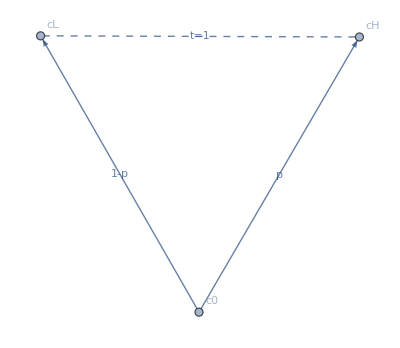

```mathematica
Graph[{Labeled[c0->cH,"p"],Labeled[c0->cL,"1-p"],Labeled[cH<->cL,"t=1"]},VertexLabels->"Name",EdgeStyle->{cH<->cL->Dashed}]
```

```mathematica
u[s][c_]:=Log[c] (* Sheila's utility for consumption *)
u[b][c_]:=Log[c] (* Bruce's utility for consumption *)
u[s][c]
u[b][c]
```

Log[c]

Log[c]

There is no production but consumers are endowed with contingent goods .

```mathematica
prices={p0,pH,pL}  (* price of contingent goods *)
basket={c0,cH,cL} (* basket of contingent goods *)
p0=1 (* always possible to normalize one of the prices to 1 *)
e[b]={10,0,0} (* endowment of Bruce *)
e[s]={0,10,10} (* endowment of Sheila *)
```

{p0,pH,pL}

{c0,cH,cL}

1

{10,0,0}

{0,10,10}

### Review Questions

Describe the basket (0,1,1).
Answer: The basket (0,1,1) is a contract that delivers one unit of consumption good in period t=1.

Describe the basket (1,0,1).
Answer: The basket (1,0,1) is a contract that delivers one unit of consumption good in period t=0 AND one unit of consumption in period t=1 if the state L happens. In particular the basket (1,0,1) delivers zero units of consumption in period t=1 when the state H happens.

Describe Bruce and Sheila’s incomes.
Answer: Their income is the value of their respective endowments.

```mathematica
prices.e[b]
prices.e[s]
```

10

10 pH+10 pL

Describe the total supply (of each contingent good) in this economy.
Answer: Since there is no production, the supply is just the sum of the consumers’ endowments. In particular, the supply of any contingent good is perfectly inelastic. In the current example the supply of is

```mathematica
e[b]+e[s] (* (supply of c0, supply of cH, supply of cL)*)
```

{10,10,10}

## Defining the Discounted Expected Utility

```mathematica
U[i]:=u[i][c0]+δ[i]*(p*u[i][cH]+(1-p)*u[i][cL])  (*the variable i indexes the consumer so i = b or s *)
```

```mathematica
U[i]
```

u[i][c0]+δ[i] (p u[i][cH]+(1-p) u[i][cL])

```mathematica
U[i]/.i->s
U[i]/.i->b
```

Log[c0]+(p Log[cH]+(1-p) Log[cL]) δ[s]

Log[c0]+(p Log[cH]+(1-p) Log[cL]) δ[b]

## Finding the Individual Demands

```mathematica
L=U[i]-λ*(prices.basket-income[i])
```

-λ (c0+cH pH+cL pL-income[i])+u[i][c0]+δ[i] (p u[i][cH]+(1-p) u[i][cL])

```mathematica
vars=Join[basket,{λ}]
grad=Grad[L,vars]
FOC=Thread[grad==0]
sysb=FOC/.i->b
BruceDemand=Solve[sysb,vars][[1]]
```

{c0,cH,cL,λ}

{-λ+u[i]'[c0],-pH λ+p δ[i] u[i]'[cH],-pL λ+(1-p) δ[i] u[i]'[cL],-c0-cH pH-cL pL+income[i]}

{-λ+u[i]'[c0]==0,-pH λ+p δ[i] u[i]'[cH]==0,-pL λ+(1-p) δ[i] u[i]'[cL]==0,-c0-cH pH-cL pL+income[i]==0}

{1/c0-λ==0,-pH λ+(p δ[b])/cH==0,-pL λ+((1-p) δ[b])/cL==0,-c0-cH pH-cL pL+income[b]==0}

{c0→income[b]/(1+δ[b]),cH→(p income[b] δ[b])/(pH (1+δ[b])),cL→(income[b] δ[b]-p income[b] δ[b])/(pL (1+δ[b])),λ→(1+δ[b])/income[b]}

```mathematica
syss=FOC/.i->s
SheilaDemand=Solve[syss,vars][[1]]
```

{1/c0-λ==0,-pH λ+(p δ[s])/cH==0,-pL λ+((1-p) δ[s])/cL==0,-c0-cH pH-cL pL+income[s]==0}

{c0→income[s]/(1+δ[s]),cH→(p income[s] δ[s])/(pH (1+δ[s])),cL→(income[s] δ[s]-p income[s] δ[s])/(pL (1+δ[s])),λ→(1+δ[s])/income[s]}

## Finding equilibrium prices

#### Market Clearing conditions

Endowments:

```mathematica
e[b]
e[s]
```

```mathematica
e[b]+e[s] (* mkt supply, inelastic!*)
```

{10,10,10}

```mathematica
mktclear={(c0/.BruceDemand)+(c0/.SheilaDemand)==e[b][[1]]+e[s][[1]],(cH/.BruceDemand)+(cH/.SheilaDemand)==e[b][[2]]+e[s][[2]]} (* Demand of c0 == Supply of c0, Demand of cH == Supply of cH, you can pick any two markets since we are solving for two prices. pH and pL.*)
```

{income[b]/(1+δ[b])+income[s]/(1+δ[s])==10,(p income[b] δ[b])/(pH (1+δ[b]))+(p income[s] δ[s])/(pH (1+δ[s]))==10}

Remember the incomes are now endogenous. They are the value of endowments (endowment quantities times respective prices) and prices are now endogenous.

```mathematica
MKTClear=mktclear/.{income[b]->prices.e[b],income[s]->prices.e[s]}
```

{10/(1+δ[b])+(10 pH+10 pL)/(1+δ[s])==10,(10 p δ[b])/(pH (1+δ[b]))+(p (10 pH+10 pL) δ[s])/(pH (1+δ[s]))==10}

```mathematica
EquilibriumPrices=Solve[MKTClear,{pH,pL}][[1]]
```

{pH→(p δ[b] (1+δ[s]))/(1+δ[b]),pL→-1/(1+δ[b])(-δ[b]+p δ[b]-δ[b] δ[s]+p δ[b] δ[s])}

```mathematica
EqPrices=Simplify[EquilibriumPrices]
```

{pH→(p δ[b] (1+δ[s]))/(1+δ[b]),pL→-((-1+p) δ[b] (1+δ[s]))/(1+δ[b])}

```mathematica
Simplify[D[x/(1+x),x]]
```

1/(1+x)^2

### Finding Equilibrium Quantities

```mathematica
BruceQuantities=Simplify[basket/.BruceDemand/.income[b]->prices.e[b]/.EqPrices]
SheilaQuantities=Simplify[basket/.SheilaDemand/.income[s]->prices.e[s]/.EqPrices]
```

{10/(1+δ[b]),10/(1+δ[s]),10/(1+δ[s])}

{(10 δ[b])/(1+δ[b]),(10 δ[s])/(1+δ[s]),(10 δ[s])/(1+δ[s])}

# Financial Market Economy

```mathematica
basket
e[b]
e[s]
```

{c0,cH,cL}

{10,0,0}

{0,10,10}

We assume two financial assets
1) a bond (B) issued in period zero with return r in period one
2) an asset (A) issued in period zero with return s in period one/state H and return zero in period one/state L.

```mathematica
budget[i_]:={c0->e[i][[1]]-zA[i]-zB[i],cH->e[i][[2]]+r*zB[i]+s*zA[i],cL->e[i][[3]]+r*zB[i]+0*zA[i]}
```

Part::partw: Part 2 of e[a] does not exist.

Part::partw: Part 3 of e[a] does not exist.

Part::partw: Part 2 of e[b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{(c0→a-zA[a]-zB[a])+(c0→b-zA[b]-zB[b]),(cH→e[a]⟦2⟧+s zA[a]+r zB[a])+(cH→e[b]⟦2⟧+s zA[b]+r zB[b]),(cL→e[a]⟦3⟧+r zB[a])+(cL→e[b]⟦3⟧+r zB[b])}

```mathematica
U[i]/.{i->b}/.budget[b]
```

Log[10-zA[b]-zB[b]]+((1-p) Log[r zB[b]]+p Log[s zA[b]+r zB[b]]) δ[b]

```mathematica
U[i]/.{i->s}/.budget[s]
```

Log[-zA[s]-zB[s]]+((1-p) Log[10+r zB[s]]+p Log[10+s zA[s]+r zB[s]]) δ[s]

```mathematica
Ub=U[i]/.{i->b}/.budget[b]
```

Log[10-zA[b]-zB[b]]+((1-p) Log[r zB[b]]+p Log[s zA[b]+r zB[b]]) δ[b]

```mathematica
Us=U[i]/.{i->b}/.budget[s]
```

Log[-zA[s]-zB[s]]+((1-p) Log[10+r zB[s]]+p Log[10+s zA[s]+r zB[s]]) δ[b]

```mathematica
cvarsb={zA[b],zB[b]}
```

{zA[b],zB[b]}

```mathematica
cvarss={zA[s],zB[s]}
```

{zA[s],zB[s]}

```mathematica
zbruce=Solve[Thread[Grad[Ub,cvarsb]==0],cvarsb][[1]]
```

{zA[b]→(10 (r δ[b]-p s δ[b]))/((r-s) (1+δ[b])),zB[b]→(10 (-s δ[b]+p s δ[b]))/((r-s) (1+δ[b]))}

```mathematica
zsheila=Solve[Thread[Grad[Us,cvarss]==0],cvarss][[1]]
```

{zA[s]→(10 (r δ[b]-p s δ[b]))/(r (r-s) (1+δ[b])),zB[s]→-(10 (r-s+r δ[b]-p s δ[b]))/(r (r-s) (1+δ[b]))}

```mathematica
financialmktclear={zA[b]+zA[s]==0,zB[b]+zB[s]==0}
```

{zA[b]+zA[s]==0,zB[b]+zB[s]==0}

```mathematica
FinMktClear=financialmktclear/.zbruce/.zsheila
```

{(10 (r δ[b]-p s δ[b]))/((r-s) (1+δ[b]))+(10 (r δ[b]-p s δ[b]))/(r (r-s) (1+δ[b]))==0,-(10 (r-s+r δ[b]-p s δ[b]))/(r (r-s) (1+δ[b]))+(10 (-s δ[b]+p s δ[b]))/((r-s) (1+δ[b]))==0}

```mathematica
Solve[FinMktClear,{r,s}]
```

{{r→1/δ[b],s→1/(p δ[b])}}

```mathematica
Exit[]
```

```mathematica
rA={-1,2,2}
rB={-1,4,1}
rC={-1,1,4}
```

{-1,2,2}

{-1,4,1}

{-1,1,4}

```mathematica
w={wA,wB,WC}
```

{wA,wB,WC}

```mathematica
10*x+9*y == 10*ex+9*ey
```

```mathematica
x+0.9*y == ex+0.9*ey
```